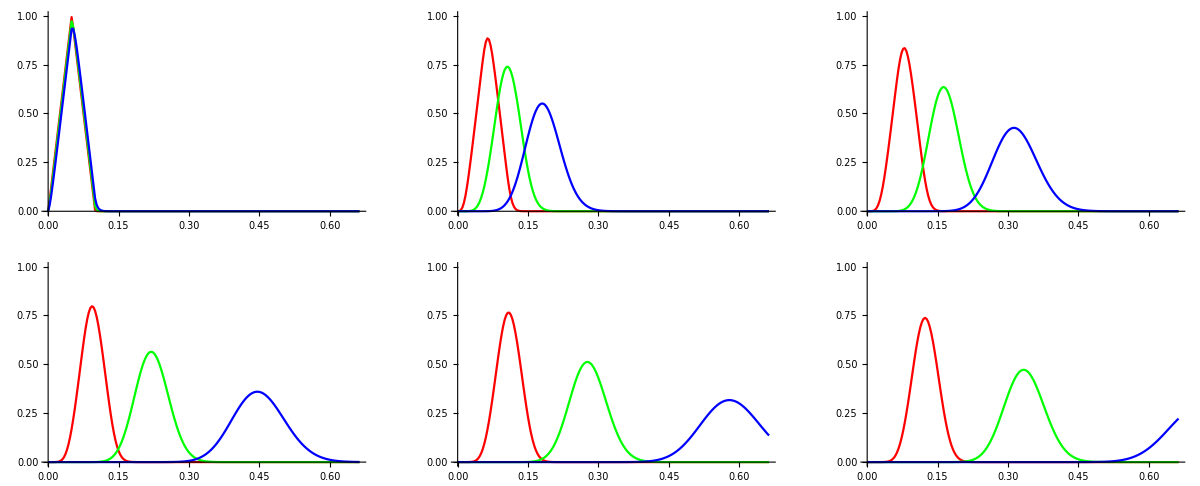

```mathematica
(* MA39110 / Assignment 10 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
Model[n0_,nu0_,t0_]:=Module[{n=100*n0,nu=nu0,t=t0},
x0=0;xf=10;h=(xf-x0)/n;
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
f[x_]=UnitTriangle[20x-1];
PLT=Table[Table[0,{y,0,n}],{x,1,n+1}];
U=Table[f[XT[[x]]],{x,1,n+1}];
UT=U;
For[j=1,j≤t,j++,{
For[i=2,i<n,i++,
{
U=UT;
UT[[i]]=(1-nu)U[[i]]+nu*U[[i-1]]
}];
PLT[[j]]=U;
}];
PLT
];
sol1=Model[30,0.1,200];
sol2=Model[30,0.3,200];
sol3=Model[30,0.5,200];
Rotate[GraphicsGrid[{{Show[{ListLinePlot[Transpose[{XT,sol1[[1]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[1]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[1]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}],Show[{ListLinePlot[Transpose[{XT,sol1[[40]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[40]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[40]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}],Show[{ListLinePlot[Transpose[{XT,sol1[[80]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[80]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[80]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}]},
{Show[{ListLinePlot[Transpose[{XT,sol1[[120]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[120]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[120]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}],Show[{ListLinePlot[Transpose[{XT,sol1[[160]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[160]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[160]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}],Show[{ListLinePlot[Transpose[{XT,sol1[[200]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Red]},{ListLinePlot[Transpose[{XT,sol2[[200]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Green]},{ListLinePlot[Transpose[{XT,sol3[[200]]}][[1;;200;;1]],PlotRange->{0,1},PlotStyle->Blue]}]}}],Pi/2]
```